# Definitions (evaluate this part first... should happen automatically.)

```mathematica
Needs["QuantumInformation`"];
Needs["MaTeX`"];
```

#### General functions

```mathematica
evalTimePlot[ ham_, {t_,t1_,t2_} ] :=Module[{varts, evalVsT},
	varts = Range[ t1, t2, (t2-t1)/100 ];
	evalVsT = Table[ {ConstantArray[ vart, Length@ham], Sort@Eigenvalues[N[ ham /. t-> vart ]] }ᵀ, {vart, varts}];
	Return[evalVsTᵀ];
];
```

#### Star Graphs

```mathematica
(* The function "w" is free: for later use, time-dependent functions can be plugged in (or just supply an undefined variable) *)

xx[a_, b_, w_ ] := {{0, w[a, b]}, {w[a, b], 0}};
starGraph[ narms_, larm_, w_ ] := Module[{mjIdx, nq, listOfParams, graph, s},
   mjIdx[ m_, j_ ] := m*larm + j;
   nq =  larm *narms + 1;
   
   listOfParams = {};
   graph = ConstantArray[0, {nq, nq}];
   
   (* Loop over (m,j): m indexes the arm, j the distance on the arm *)
   Do[
    Do[
     	(* Connect the chain: *)
     	s = mjIdx[ m, j ];
     	graph[[s ;; s + 1, s ;; s + 1]] = xx[s, s + 1, w];
     	AppendTo[ listOfParams, w[s, s + 1] ];
     	, {j, 1, larm - 1}
     ];
    (* Connect the last element of the chain to the center: *)
    s  = mjIdx[m, larm];
    graph[[ s, nq]] = w[s, nq];
    graph[[ nq, s]] = w[s, nq];
    AppendTo[ listOfParams, w[s, nq] ];
    , {m, 0, narms - 1}
    ];
   
   Return[{graph, listOfParams}]
];
```

#### Random bip graphs

```mathematica
RandomBooleans[ v1_, v2_, p_:.5 ] := ArrayReshape[ Boole@Map[ # < p &,   RandomReal[ 1, v1*v2 ] ] , {v1,v2} ] ;

RandBipGraph[ v1_, p_ ] := Module[{B,Bw,A,Aw},
	B = RandomBooleans[ v1, v1-1, p ] ;
	Bw = RandomReal[ 1, Dimensions[B] ] * B;
	A = ArrayFlatten[ {{0, B}, {Bᵀ, 0}} ] ;
	Aw = ArrayFlatten[ {{0, Bw}, {Bwᵀ, 0}} ] ;
	Return[ {A,Aw} ];
];

PerfectMatchQ[ A_ ]:= Length[  SparseArray`MaximalBipartiteMatching[ A  ]] == Length[A];
smallestEvalBip[ Asquare_ ]:= Sort[ Eigenvalues[ N [ Asquare ] ] ][[ Ceiling[Length[Asquare]/2 + 1] ]];

matchAndDetCondition[ Aw_ , a_, b_ ]:= Module[{Amina, Aminb},
	Amina = Aw[[ Delete[ Range[ Length[Aw] ], a ] , Delete[ Range[ Length[Aw] ], a   ]  ]];
	Aminb = Aw[[ Delete[ Range[ Length[Aw] ], b ] , Delete[ Range[ Length[Aw] ], b   ]  ]];

	Return[{ 
		PerfectMatchQ[ Amina ], PerfectMatchQ[ Aminb ]
			, Abs[Det[Amina]],  Abs[Det[Aminb]]
			, smallestEvalBip[Amina], smallestEvalBip[Aminb]
		}];
];

simulationError[ Aw_, a_, b_, T_, wafun_, wbfun_, t_ ] := Module[ {Actrl, state, err},
	Actrl = Aw;
	Actrl[[a]] = Aw[[a]] * wafun;
	Actrl[[All,a]] = Aw[[a]] * wafun;
	Actrl[[b]] = Aw[[b]] * wbfun;
	Actrl[[All,b]] = Aw[[b]] * wbfun;

	state = evolveState[ Actrl, Vec[a-1,Length[Aw]], {t,0,T} ][T];  (* Note that Vec counts from 0, but a/b given as 1,2,3,... etc *)
	err = 1- Abs[state.Vec[b-1,Length[Aw] ]]; (* No conjugation needed for basis state |b> *)

	Return[err];
];
```

#### Hex grids

```mathematica
(* We define the lattice as follows:
- Take a two-site unit cell, placed horizontally.
- The parameter w(idth) tells us how many vertices fit in the horizontal dimension .
- The parameter h(eight) tells us how many horizontal layers to stack.

From there onwards, we connect the horizontal layers using the conventional brick stone construction. See small graphs for an example. 

For CTAP, one needs an ODD number ofites: Hence some site must be removed (typically the bottom-right, which is dangling anyway).
*)

hexagonalLattice[w_, h_ ]:= Module[{n,A,x,y, i1, i2},
n = 2*w*h;
A = ConstantArray[0, {n,n}];

(* Add in-cell connections *)
Do[ A[[j,j+1]] = 1;  A[[j+1,j]] = 1;, {j,1,n,2} ];

(* Add connections to the east *)
Do[ (* Loop over all vertical rows y *)
Do[ (* Loop over all horizontal connections (x) *)
i1 = 2w(y-1) + 2x;
i2 = i1 + 1;
A[[i1,i2]] = 1 ;
 A[[i2,i1]] = 1;
,{x,1,w-1}]
,{y,1,h}];

(* Add connections to the south *)
Do[ (* Loop over all vertical rows y *)
Do[ (* Loop over all horizontal connections (x) *)
i1 = 2w(y-1) + 2x;
i2 = 2w y + (2x - 1 );
A[[i1,i2]] = 1 ;
 A[[i2,i1]] = 1;
,{x,1,w}]
,{y,1,h-1}];

Return[A];
];

(* The simulationError function is meant to test CTAP on arbitrary adjacency matrices Aw. Transfer happens from site a to b (give the indices of these states as integers). Output is 1-|<a|U|b>|. *)
simulationError[ Aw_, a_, b_, T_, wafun_, wbfun_, t_ ] := Module[ {Actrl, state, err},
Actrl = Aw;
Actrl[[a]] = Aw[[a]] * wafun;
Actrl[[All,a]] = Aw[[a]] * wafun;
Actrl[[b]] = Aw[[b]] * wbfun;
Actrl[[All,b]] = Aw[[b]] * wbfun;

state = evolveState[ Actrl, Vec[a-1,Length[Aw]], {t,0,T} ][T];  (* Note that Vec counts from 0, but a/b given as 1,2,3,... etc *)
err = 1- Abs[state.Vec[b-1,Length[Aw] ]]; (* No conjugation needed for basis state |b> *)

Return[err];
];
```

#### Randomizing graphs

```mathematica
randomOrthogonal[ n_ ]:= Module[{a,b},
	a = Table[
			Which[x == y, RandomReal[], x < y, RandomReal[], x > y, 0],
		{x, n}, {y, n}]; 
	b = Table[
			If[x <= y, a[[x, y]], Conjugate[a[[y, x]] ]], 
		{x, n}, {y, n}];
	Return[b];
];

randomHermitean[ n_ ]:= Module[{a,b},
	a = Table[
			Which[x == y, RandomReal[], x < y, RandomComplex[], x > y, 0],
		{x, n}, {y, n}]; 
	b = Table[
			If[x <= y, a[[x, y]], Conjugate[a[[y, x]] ]], 
		{x, n}, {y, n}];
	Return[b];
];

(* change amplitudes of h by a factor in [0,2] (e.g. a real number *)
perturbHermitean[ h_, rndRange_:{-2,2} ]:= Module[{n, new},
	n = Length@h;
	new = ConstantArray[ 0, {n,n}];
	Do[If[ h[[x,y]] ≠ 0, 
			new[[x,y]] = h[[x,y]] * RandomReal[rndRange];
			new[[y,x]] = Conjugate[new[[x,y]] ];
		];
	,{x,1,n},{y,1,x}];
	Return[new];
];
```

# CTAP on Star Graphs

#### Definitions

```mathematica
starGraph[ 3,3, f][[1]] // MatrixForm
```

(0 | f[1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
f[1,2] | 0 | f[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | f[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | f[3,10]
0 | 0 | 0 | 0 | f[4,5] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | f[4,5] | 0 | f[5,6] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | f[5,6] | 0 | 0 | 0 | 0 | f[6,10]
0 | 0 | 0 | 0 | 0 | 0 | 0 | f[7,8] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | f[7,8] | 0 | f[8,9] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | f[8,9] | 0 | f[9,10]
0 | 0 | f[3,10] | 0 | 0 | f[6,10] | 0 | 0 | f[9,10] | 0)

## Eigenvalue statistics

#### Weights all equal to 1.

For various settings, we will store 1) the DET with OUTSIDE or MIDDLE qubit removed, and 2) the GAP of the fully coupled system.

Conclusion: 
The DET is always +-1
The GAP does not change as a function of narms, only as a function of larm.

```mathematica
giveDets[ g_ ]:= {Det[g[[2;;, 2;;]] ], Det[g[[;;-2,;;-2]] ]  };
giveGap[ g_ ]:= Sort[ Eigenvalues[ N[g] ] ]⟦  Ceiling[ Length[g]/2 ]+1 ⟧;
```

{{{1,1},{1,1},{1,1},{1,1}},{{-1,-1},{1,1},{-1,-1},{1,1}},{{1,1},{1,1},{1,1},{1,1}},{{-1,-1},{1,1},{-1,-1},{1,1}},{{1,1},{1,1},{1,1},{1,1}},{{-1,-1},{1,1},{-1,-1},{1,1}},{{1,1},{1,1},{1,1},{1,1}}}

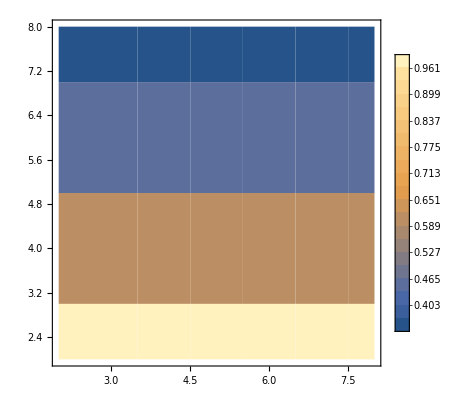

```mathematica
narmss = Range[2,8];
larmss = Range[2,8,2];

res = Table[ 
{g,l} = starGraph[ narms, larm, w ];
uniformParams = Table[ p -> 1, {p,l} ];
{narms, larm,  giveDets[ g /. uniformParams ], giveGap[ g/. uniformParams ] }
, {narms, narmss}, {larm, larmss} ];

(* Instepcting the DETs *)
res[[All,All,3]]

(* Inspecting the gaps *)
gaps = ArrayReshape[ res[[All, All, {1,2,4} ]], {Length@narmss * Length@larmss, 3 } ];
ListContourPlot[gaps, InterpolationOrder->0, Contours->20, PlotLegends->Automatic]
```

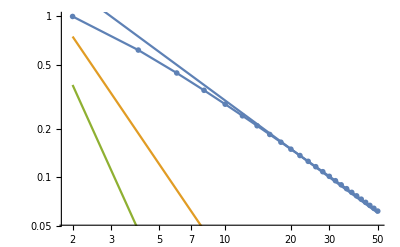

```mathematica
larmss = Range[2,50,2];
narms = 2;
res = Table[ 
{g,l} = starGraph[ narms, larm, w ];
uniformParams = Table[ p -> 1, {p,l} ];
 {larm, giveGap[ g/. uniformParams ]}
,{larm, larmss} ];

decayplts = Table[ 3 t^{-j}, {j,1,3}];
Show[{
ListLogLogPlot[res]
,LogLogPlot[ Evaluate@( decayplts), {t,Min[larmss], Max[larmss]}  ]
}]
```

## Actual simulations

#### Definitions

```mathematica
gapVsTime[ narms_, larms_,T_, wafun_, wbfun_ ] := Module[
	{g,l,w,nq,uniformParams,wa,wb,setwa,setwb,hamt, varts, evalVsT},
	{g,l} = starGraph[narms, larms, w  ];
	nq = narms*larms + 1;
	uniformParams = Table[ p -> 1, {p,l} ];
	wa = {w[1,2]};
	wb = Table[ i = larms+ m * larms ; w[i, nq] , {m,0, narms-1} ];
	setwa = Table[ p -> wafun , {p,wa}];
	setwb = Table[ p -> wbfun , {p, wb} ];
	hamt = g /. setwa /. setwb /. uniformParams;

	varts = Range[ 0, T, T/100 ];
	evalVsT = Table[ 
	{ConstantArray[ vart, nq], Sort@Eigenvalues[N[ hamt /. t-> vart ]] }ᵀ
	, {vart, varts}];

	Return[evalVsT];
];

simulationError[ narms_, larms_, T_, wafun_, wbfun_ ] := Module[ {g,l,w,nq,uniformParams,wa,wb,setwa,setwb,hamt,state,err},
	{g,l} = starGraph[narms, larms, w  ];
	nq = narms*larms + 1;

	uniformParams = Table[ p -> 1, {p,l} ];
	wa = {w[1,2]};
	wb = Table[ i = larms+ m * larms ; w[i, nq] , {m,0, narms-1} ];
	setwa = Table[ p -> wafun , {p,wa}];
	setwb = Table[ p -> wbfun , {p, wb} ];

	hamt = g /. setwa /. setwb /. uniformParams;
	state = evolveState[ hamt, Vec[0,nq], {t,0,T} ][T];
	err = 1- Abs[state.Vec[nq-1,nq]]; (* No conjugation needed for basis state |nq> *)

	Return[err];
];
```

#### Simulation error vs narmss, larmss

```mathematica
narmss = Range[2,40];
larmss = Range[2,2,2];
T=  30;
wafun = t/T;
wbfun = 1-t/T;

res = Table[
{narms, larms, simulationError[ narms, larms, T, wafun, wbfun ]}
,{narms, narmss}, {larms, larmss}];
reslist = ArrayReshape[ res, {Length@larmss * Length@narmss, 3 } ];

logreslist = reslist;
logreslist[[All,3]] = Log@reslist[[All,3]];
```

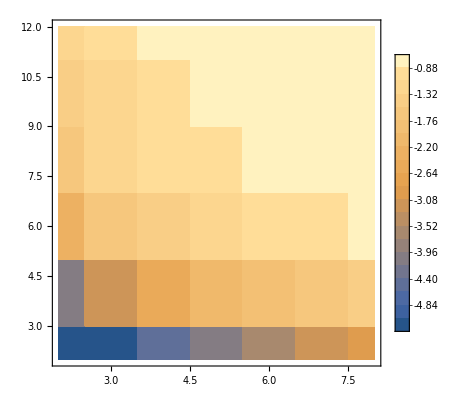

```mathematica
ListContourPlot[ logreslist, InterpolationOrder->0, Contours->20 , PlotLegends->Automatic ]
```

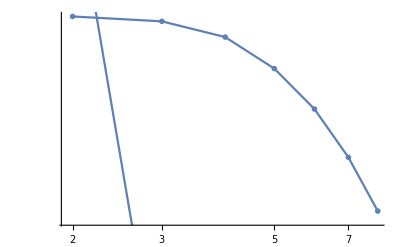

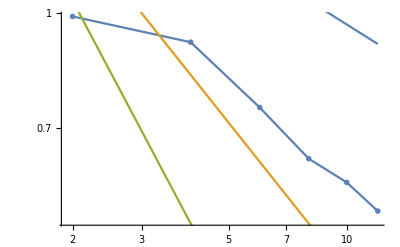

```mathematica
(* DECAY WITH NARMSS *)
fids = res;
fids[[All,All,3]] = 1-res[[All,All,3]];
decayplts = Table[ 1.3 t^{-j/3}, {j,1,3}];

Show[{
ListLogLogPlot[fids[[All,1,{1,3}]] ]
,LogLogPlot[ Evaluate@(  decayplts), {t,Min[narmss], Max[narmss]}  ]
}]

(* DECAY WITH LARMS *)
Show[{
ListLogLogPlot[fids[[3, All,{2,3}]] ]
,LogLogPlot[ Evaluate@(1.6*  decayplts), {t,Min[larmss], Max[larmss]}  ]
}]
```

#### Spectra over time

energies DO differ over time, but the range is negligible.

```mathematica
narmss = Range[2,8];
larmss = Range[2,12,2];
```

```mathematica
res = gapVsTime[ 4, 5, 1, wafun, wbfun ];
```

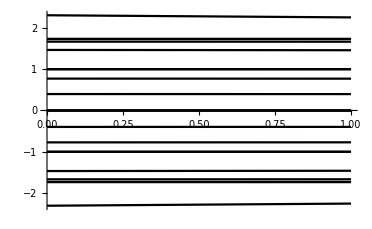

```mathematica
ListPlot[ resᵀ, PlotMarkers->None, PlotStyle->Black]
```

```mathematica
res // Dimensions
```

{101,21,2}

```mathematica
Min@res[[All, 1, 2 ]]
Max@res[[All, 1, 2 ]]
```

-2.30615

-2.25459

```mathematica
Min@res[[All, 18, 2 ]]
Max@res[[All, 18, 2 ]]
```

1.66555

1.66647

# CTAP on random bipartite lattices

TEST if it works:

```mathematica
v1 = 3;
p = .5;  (* Prob. of vertex connection *)
T = 1000;
wafun = t/T;
wbfun = 1-t/T;
{a,b} = {1,2};

{A,Aw} = RandBipGraph[ v1, p ];

(* Find the simulation error, and check if requirements are fulfilled *)
simulationError[ Aw, a,b, T, wafun, wbfun, t ]
matchAndDetCondition[ Aw, a, b ]
```

0.037916

{True,True,0.209089,0.00163605,0.523648,0.0483428}

LOOP over a heap of cases:

```mathematica
v1s = {3,6, 10};
ps = {.4, .8, 1};
nwtsamples = 10;
T = 100;
wafun = t/T;
wbfun = 1-t/T;
{a,b} = {1,2};

res = Table[
{A,Aw} = RandBipGraph[ v1, p ];

(* Find the simulation error, and check if requirements are fulfilled *)
{simulationError[ Aw, a,b, T, wafun, wbfun, t ], matchAndDetCondition[ Aw, a, b ] }

, {v1,v1s}, {p,ps}, nwtsamples ];
```

```mathematica
res // Dimensions
```

```mathematica
{3,2,10,2}
```

{3,2,10,2}

```mathematica
res[[-1,1]] // MatrixForm
```

(1. | {False,False,0.,0.,2.7451×10^-16,0.}
0.537671 | {False,False,0.,0.,-3.13913×10^-16,5.12967×10^-16}
0.993269 | {False,False,0.,0.,-1.97592×10^-17,6.85318×10^-17}
0.9822 | {False,False,0.,0.,-9.43157×10^-18,7.53291×10^-33}
0.998084 | {False,False,0.,0.,8.88193×10^-16,1.35146×10^-17}
0.95646 | {False,False,0.,0.,0.,0.}
1. | {False,False,0.,0.,2.20437×10^-19,0.}
0.824569 | {False,False,0.,0.,4.55682×10^-17,2.38144×10^-16}
0.981746 | {False,False,0.,0.,2.73595×10^-16,1.71951×10^-16}
0.659424 | {False,False,0.,0.,2.2231×10^-16,2.25077×10^-16})

For each value of {v1, p}, we want to know:
1. Fraction of FAIL events; and count the number of succesful transfers. 
2. Fraction of GOOD events -> avg fidelity.

```mathematica
(* How often are cases satisfied? *)
satisfied = Table[ And @@ res[[ v1idx, pidx, sampidx, 2, {1,2} ]]
,{v1idx, Length@v1s}, {pidx, Length@ps}, {sampidx, nwtsamples} ];
totalSatisfied = Total[ Boole@satisfied , {3} ];
totalSatisfied // MatrixForm
```

(4 | 6 | 10
3 | 10 | 10
9 | 10 | 10)

```mathematica
(* Loop through all results... and separate the SATISFIED and UNSATISFIED results. *)
sat = {};
unsat = {};

Do[
If[ And@@res[[v1idx, pidx, sampidx, 2, {1,2} ]] 
, AppendTo[  sat , {v1s[[v1idx]], ps[[pidx]], res[[v1idx, pidx, sampidx]]} ]
, AppendTo[  unsat , {v1s[[v1idx]], ps[[pidx]], res[[v1idx, pidx, sampidx]]} ]
];

,{v1idx, Length@v1s}, {pidx, Length@ps}, {sampidx, nwtsamples} ];
```

```mathematica
(* Some UNSAT cases turn out to have proper transfer.... due to Symmetry?! *)
unsat
```

{{3,0.4,{0.00312329,{False,False,0.,0.,0.,0.}}},{3,0.4,{1.,{True,False,0.0165884,0.,0.162285,6.17995×10^-17}}},{3,0.4,{1.,{False,False,0.,0.,0.,0.}}},{3,0.4,{1.,{False,True,0.,0.157123,0.,0.534001}}},{3,0.4,{1.,{True,False,0.0181251,0.,0.145294,1.23165×10^-16}}},{3,0.4,{1.,{False,True,0.,0.00068143,0.,0.0333561}}},{3,0.8,{0.0225649,{False,True,0.,1.12737×10^-6,0.,0.000911937}}},{3,0.8,{1.,{True,False,0.023174,0.,0.113023,5.45409×10^-18}}},{3,0.8,{0.792014,{False,False,0.,0.,0.,0.}}},{3,0.8,{1.,{True,False,0.000246276,0.,0.0163905,0.}}},{6,0.4,{1.,{False,False,0.,0.,2.57184×10^-16,2.57184×10^-16}}},{6,0.4,{0.000605969,{False,False,0.,0.,5.45883×10^-19,2.22368×10^-16}}},{6,0.4,{0.568239,{True,False,0.0000645542,0.,0.0286241,6.66141×10^-16}}},{6,0.4,{0.354047,{False,False,0.,0.,8.20523×10^-19,6.2208×10^-17}}},{6,0.4,{1.,{True,False,0.000567559,0.,0.0361757,0.}}},{6,0.4,{1.,{False,False,0.,0.,-6.21549×10^-18,4.66641×10^-16}}},{6,0.4,{1.,{False,True,0.,2.63334×10^-10,0.,0.0000538826}}},{10,0.4,{1.,{False,True,0.,0.00258587,0.,0.0699035}}}}

```mathematica
(* For SAT cases, we expect all transfer fidelities to be reasonable! *)

(* Select specific cases *)
v1val = 10;
pval = 1;
selected = Select[ sat, #[[1]] == v1val && #[[2]] == pval  & ];
selectederr = selected[[All,3,1]]
selectedgap1 = selected[[All,3,2,3]]
selectedgap2 = selected[[All,3,2,4]]
```

{0.106186,0.0502153,0.455006,0.00903628,0.173643,0.145046,0.502469,0.00236982,0.631562,0.104253}

{0.000100811,0.000245334,0.0000782289,0.000526041,0.000548886,0.000235597,0.000526717,0.000137221,0.0000175199,0.00242809}

{0.000025264,0.000715239,0.00174229,0.00069051,0.000341518,0.000085038,0.00103651,0.000195063,0.000260371,0.00565593}

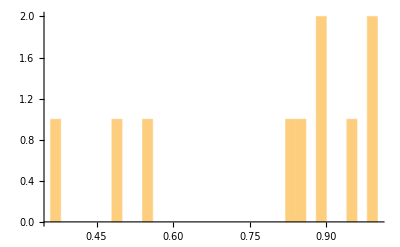

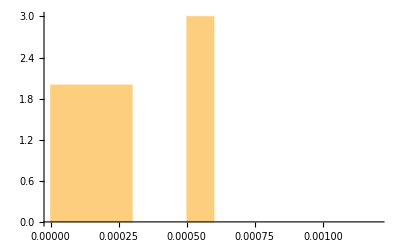

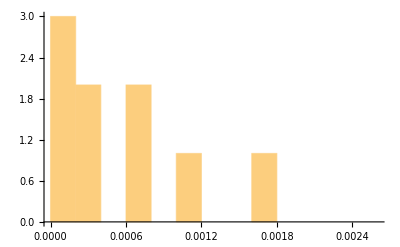

```mathematica
Histogram[ 1-selectederr , 20 ]
Histogram[ selectedgap1 , 20 ]
Histogram[ selectedgap2 , 20 ]
```

Conclusion: The results here are rather bad: there is often an eigenvector close to 0 that screws up the protocol.
On the other hand, with a small number of random samples one might find a “good” configuration.

# CTAP on Hexagonal Grids

#### Test if CTAP works

```mathematica
ws = Range[2,6];
hs = Range[2,6];
T0 = 1000; 

res = Table[ 
nq = w*h*2 - 1;
T= T0 ;
A = hexagonalLattice[w,h][[;;-2,;;-2]];
simulationError[ A, 1, nq, T, t/T, 1-t/T, t ]
,{w,ws}, {h,hs} ]
```

{{9.95099×10^-6,0.0000826171,0.000443076,0.00209863,0.00691485},{0.0000826171,0.00135251,0.0144325,0.0954499,0.252928},{0.000443076,0.0144325,0.167516,0.430458,0.629692},{0.00209863,0.0954499,0.430458,0.688758,0.824646},{0.00691485,0.252928,0.629692,0.824646,0.911474}}

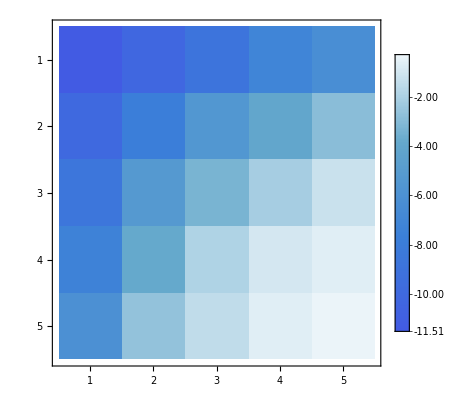

```mathematica
MatrixPlot[ Log@res, PlotLegends-> Automatic ]
```

Between different locations on the graph. 

For a {w,h} = {3,3}, let as = Range[1,nq,2] (counting only the vertices in V1, using brickstone grid, first horizontally, then vertically. 

We find that transfer to places 2,3,4 is pretty good (these are close to 1), and to 5 is interesting because it’s the exact middle.
For some reason, site 9 performs badly.

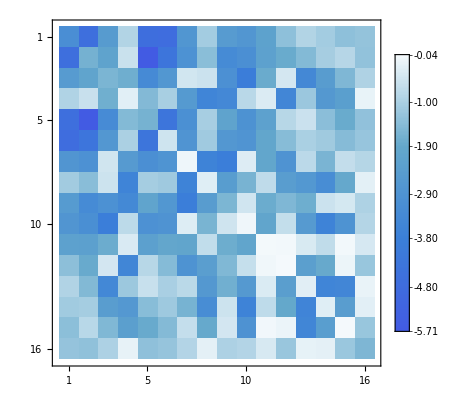

{{5,2}}

{{15,15}}

```mathematica
{w,h} = {4,4};
A = hexagonalLattice[w,h][[;;-2,;;-2]];
nq = 2*w*h-1;

as = Range[ 1,nq, 2];
bs = Range[ 1,nq, 2];
T = 100;

sendrecfids = Table[
simulationError[ A, a,b, T, t/T, 1-t/T, t ] 
,{a,as},{b,bs}];

MatrixPlot[ Log@sendrecfids, PlotLegends->Automatic ]

Position[ sendrecfids, Min@ sendrecfids ]
Position[ sendrecfids, Max@ sendrecfids ]
```

```mathematica
sendrecfids[[4,13]]
```

0.694098

```mathematica
sendrecfids[[5,2]]
```

0.00331182

#### Plotting E-levels (whatever current A is)

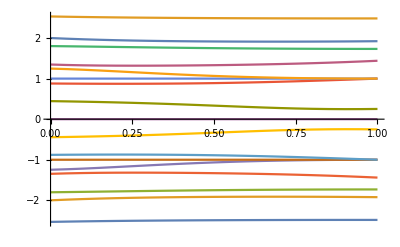

```mathematica
T = 1;
tvals = Range[0,1,T/20];

a = 1;
b= 3;

Aw = A;
Actrl = Aw;
Actrl[[a]] = Aw[[a]] * t/T;
Actrl[[All,a]] = Aw[[a]] * t/T;
Actrl[[b]] = Aw[[b]] * (1-t/T);
Actrl[[All,b]] = Aw[[b]] * (1-t/T);

evalvst = Table[ 
{ConstantArray[tval,Length[Actrl]],Chop@Sort@Eigenvalues@N@(Actrl /. t-> tval)}ᵀ
,{tval,tvals}];
ListPlot[ evalvstᵀ, PlotMarkers->None ]
```

# All energy gaps

#### Definitions

Be sure to first evaluate the graph construction functions!

```mathematica
(* A function that automatically generates the gap scaling as a function of N, for easy plotting 

makeGraph[a,b]   <--- give a function that spits out the correct graph given optional params (a,b). 
givenq[ a, b ]   <--- calc the total number of sites given (a,b). 
nsamps           <--- if 1, then calculate for a non-weighted graph. If >1, then randomize adjacency matrix nsamps times, and take avg. 
*)

graphGapScaling[ makeGraph_, givenq_, arange_, brange_, nsamps_:1 ] := Module[{res, nq, evDidx, A, evalmean, B, resFlat},

	res = Table[
		nq = givenq[a,b];
		evDidx = Ceiling[nq/2] + 1;
	
		A = makeGraph[a,b];
		
		If[ nsamps == 1,  evalmean = (Sort@Eigenvalues[N@A])[[evDidx]],
			evalmean  = Mean@Table[  Sort[Eigenvalues[perturbHermitean[A]]][[evDidx]] , nsamps];
		];
		{nq, evalmean}
	,{a, arange}, {b,brange}];
	
	resFlat = ArrayReshape[ res, {Length@arange * Length@brange, Length[res[[1,1]] ]} ];
	Return[resFlat];
];


graphGapScaling1Par[ makeGraph_, givenq_, arange_, bfun_, nsamps_:1 ] := Module[{res, nq, b, evDidx, A, evalmean, B, resFlat},

	(* There are two graph parameters. We loop over a in "arange". Parameter b is determined as bfun[a] *)
	(* The return value is res, which consists of entries (nq, eigenvalue) *)
	res = Table[
		b = bfun[a];
		nq = givenq[a,b];
		evDidx = Ceiling[nq/2] + 1;
	
		A = N @ makeGraph[a,b];
		
		If[ nsamps == 1,  evalmean = (Sort@Eigenvalues[A])[[evDidx]],
			evalmean  = Mean@ Table[
				B = A *  RandomReal[ 1, {nq,nq} ];
				B = B + Bᵀ;
				(Sort@Eigenvalues[B])[[evDidx]]
				,nsamps];	
		];
		{nq, evalmean}
	, {a, arange}];
	
	Return[res];
];
```

### Simulating with 2 parameters (width, height)

#### HEX lattice

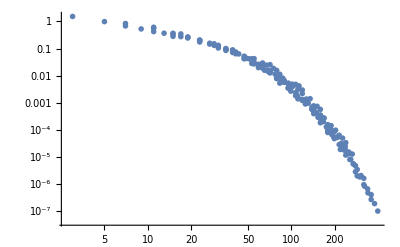

```mathematica
ws = Range[2,10];
hs = Range[1,20];
nsamps = 50;
hexnqfun[w_,h_]:= 2 * w * h -1;
hexlattfun[w_,h_]:= hexagonalLattice[w,h][[;;-2,;;-2]];

hexScalingRnd  = graphGapScaling[ hexlattfun, hexnqfun, ws, hs, nsamps ];
(* hexScaling = graphGapScaling[ hexlattfun, hexnqfun, ws, hs, 1]; *)


(* Test poly decay, using a LogLog plot: *)
ListLogLogPlot[ {hexScalingRnd}, Joined -> False ] 

(* 
(* Test Exp decay *)
Show[{
ListLogPlot[{hexScaling, hexScalingRnd}, Joined->False]
,LogPlot[  {
.1 Exp[-x/30]
, 3 * x^(-2)
}, {x,1,800}, PlotStyle->{Red,Green}]
}]
*)
```

#### STAR graph

```mathematica
narmss = Range[2,20];
larmss = Range[2,20,2];
Idfun = Function[{x,y}, 1 ] ;
nsamps = 50;
starnqfun[narms_,larms_]:=  larms *narms + 1;
starlattfun[narms_,larms_]:= starGraph[ narms, larms, Idfun  ][[1]];

starScalingRnd  = graphGapScaling[ starlattfun, starnqfun, narmss, larmss, nsamps ];
starScaling =  graphGapScaling[ starlattfun, starnqfun, narmss, larmss, 1 ];
```

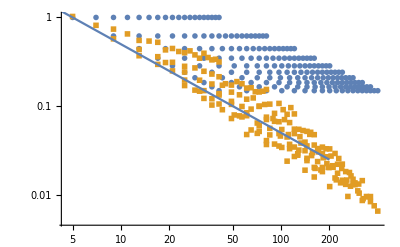

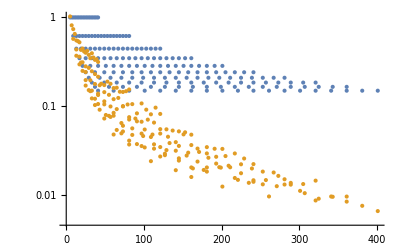

```mathematica
(* Test poly decay, using a LogLog plot: *)
Show[{
ListLogLogPlot[ {starScaling, starScalingRnd}, Joined -> False ] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

(* Test Exp decay *)
Show[{
ListLogPlot[{starScaling, starScalingRnd}, Joined->False]
}]
```

#### SQUARE grid

```mathematica
ws = Range[3,20,2];
hs = Range[1,20,2];
nsamps = 50;
squarenqfun[w_,h_]:= w*h;
squarelattfun[w_,h_]:= AdjacencyMatrix@GridGraph[ {w,h} ];

squareScalingRnd  = graphGapScaling[ squarelattfun, squarenqfun, ws, hs, nsamps ];
(* squareScaling =  graphGapScaling[ squarelattfun, squarenqfun, ws, hs, 1 ]; *)
```

Eigenvalues::arh: Because finding 105 out of the 105 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

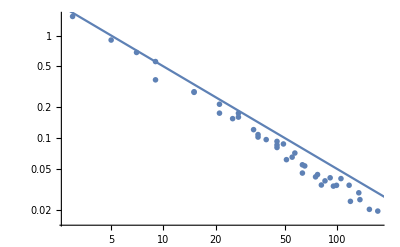

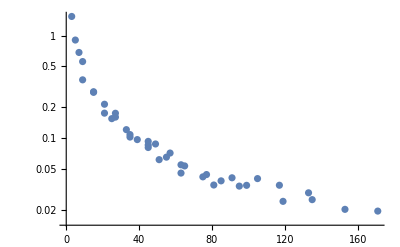

```mathematica
(* Test poly decay, using a LogLog plot: *)
Show[{
ListLogLogPlot[ { squareScalingRnd}, Joined -> False ] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

(* Test Exp decay *)
Show[{
ListLogPlot[{ squareScalingRnd}, Joined->False]
}]
```

#### Random BIP graphs

```mathematica
(* NOTE: This construction causes multiple random bip graphs to be constructed, per value of v1  *) 
vs = Round[ Range[2,250, .1] ]; 
brange = {1};
p = .8;
nsamps = 20;

bipnqfun[v1_,b_ ]:= 2 v1 - 1;
bipgraphfun[v1_, b_ ] := RandBipGraph[ v1, p ][[1]];

bipScalingRnd  = graphGapScaling[ bipgraphfun, bipnqfun, vs,brange, nsamps ];
bipScaling =  graphGapScaling[ bipgraphfun, bipnqfun, vs, brange, 1 ];
```

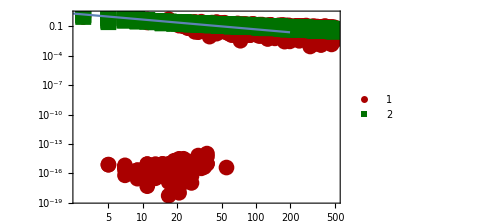

-Graphics-

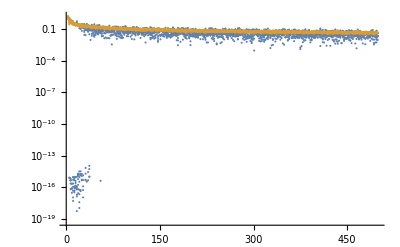

```mathematica
(* Test poly decay, using a LogLog plot: *)
Show[{
ListLogLogPlot[ { bipScaling,bipScalingRnd}, Joined -> False ] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

Show[{
ListLogLogPlot[ { bipScaling,bipScalingRnd}, Joined -> False, PlotRange->All] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

(* Test Exp decay *)
Show[{
ListLogPlot[{ bipScaling, bipScalingRnd}, Joined->False]
}]
```

#### All together

```mathematica
elementarycols = {Darker@Red, Darker@Darker@Green,  Blend[  {Darker@Red, Yellow},blend ], Blend[ {Darker@Darker@Green, Blue}, blend ] };

markers = Graphics`PlotMarkers[];
markers[[All,2]] = markers[[All,2]]*1.8;

SetOptions[ ListLogLogPlot
, BaseStyle -> {FontFamily-> Times, FontSize-> 14}
,Axes -> {False, False} 
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.001 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 15, Black ]
, FrameTicks-> Automatic
, ImageSize-> Medium
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.005] ]
, PlotMarkers -> markers
, Joined -> False
];
```

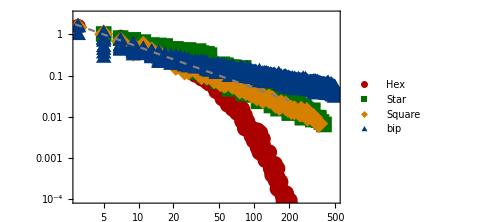

```mathematica
pltstyle = Table[  Directive[ elementarycols[[j]] ], {j,1,Length[elementarycols]}];

Show[{
ListLogLogPlot[ {hexScalingRnd, starScalingRnd, squareScalingRnd, bipScalingRnd}
 ,PlotRange->{ {3,500}, {10^-4, 3}}
, PlotLegends->{"Hex", "Star", "Square", "bip"}
, PlotStyle->pltstyle 
]
,LogLogPlot[ 5 * 1/x , {x,1,200 } , PlotStyle->{Gray, Dashed}]
}]
```

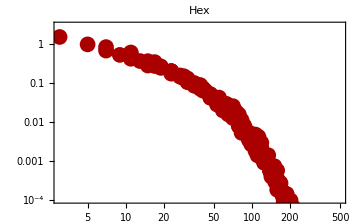
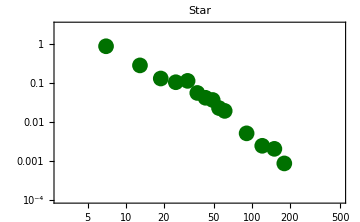
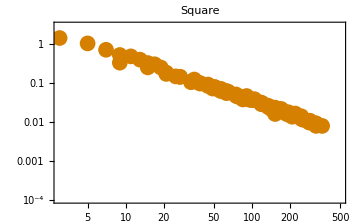
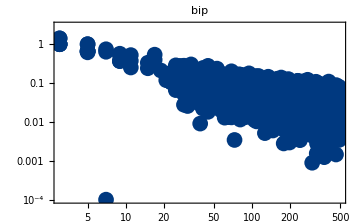

```mathematica
plts =  {hexScalingRnd, starScalingRnd, squareScalingRnd, bipScaling};
descr = {"Hex", "Star", "Square", "bip"};
pltstyle = Table[  Directive[ elementarycols[[j]] ], {j,1,Length[elementarycols]}];

plttab = Table[
ListLogLogPlot[ plts[[j]], PlotRange->{ {3,500}, {10^-4, 3}} , PlotStyle ->  pltstyle[[j]], PlotLabel->descr[[j]]  ]

,{ j, 1,Length@ plts}]
```

```mathematica
Export["gapscaling_row.pdf",Grid[ ArrayReshape[ plttab, {2,2} ]  ] ]
```

gapscaling_row.pdf

### Simulating with 1 parameter (width)

#### STAR graph

```mathematica
narmss =  {3};
larmss = Join[ Range[2,20,2], Range[ 30, 60, 10 ] ];
Idfun = Function[{x,y}, 1 ] ;
nsamps = 20;
starnqfun[narms_,larms_]:=  larms *narms + 1;
starlattfun[narms_,larms_]:= starGraph[ narms, larms, Idfun  ][[1]];

starScalingRnd  = graphGapScaling[ starlattfun, starnqfun, narmss, larmss, nsamps ];
starScaling =  graphGapScaling[ starlattfun, starnqfun, narmss, larmss, 1 ];
```

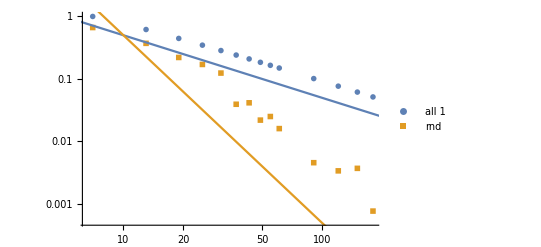

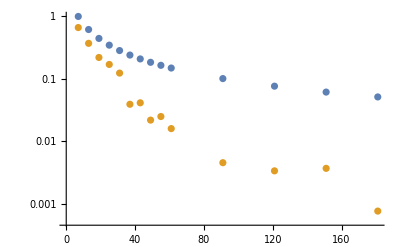

```mathematica
(* Test poly decay, using a LogLog plot: *)
Show[{
ListLogLogPlot[ {starScaling, starScalingRnd}, Joined -> False  , PlotLegends->{"all 1", "rnd"}] 
,LogLogPlot[ {5 * 1/x, 500*x^(-3)} , {x,1,200 } ]
}]

(* Test Exp decay *)
Show[{
ListLogPlot[{starScaling, starScalingRnd}, Joined->False]
}]
```

```mathematica
hexScalingRnd[[2]]
```

Part::partd: Part specification hexScalingRnd⟦2⟧ is longer than depth of object.

hexScalingRnd⟦2⟧

#### Hex Grid

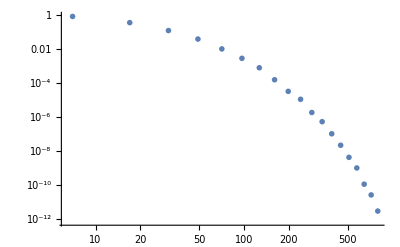

```mathematica
ws = Range[2,20];
hfun[w_]:= w;
nsamps = 50;
hexnqfun[w_,h_]:= 2 * w * h -1;
hexlattfun[w_,h_]:= hexagonalLattice[w,h][[;;-2,;;-2]];

hexScalingRnd= graphGapScaling1Par[ hexlattfun, hexnqfun, ws, hfun, nsamps ] ;
hexScaling= graphGapScaling1Par[ hexlattfun, hexnqfun, ws, hfun, 1 ] ;

(* Test poly decay, using a LogLog plot: *)
ListLogLogPlot[ {hexScalingRnd}, Joined -> False ] 

(* 
(* Test Exp decay *)
Show[{
ListLogPlot[{hexScaling, hexScalingRnd}, Joined->False]
,LogPlot[  {
.1 Exp[-x/30]
, 3 * x^(-2)
}, {x,1,800}, PlotStyle->{Red,Green}]
}]
*)
```

#### SQUARE grid

```mathematica
ws = Range[3,20,2];
hfun[w_]:= w;
nsamps = 80;
squarenqfun[w_,h_]:= w*h;
squarelattfun[w_,h_]:= AdjacencyMatrix@GridGraph[ {w,h} ];

squareScalingRnd  = graphGapScaling1Par[ squarelattfun, squarenqfun, ws, hfun, nsamps ];
(* squareScaling =  graphGapScaling[ squarelattfun, squarenqfun, ws, hs, 1 ]; *)
```

Eigenvalues::arh: Because finding 121 out of the 121 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

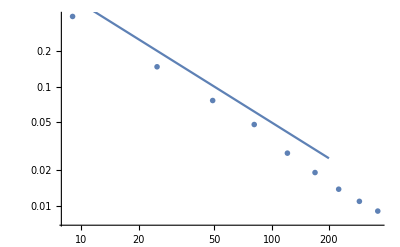

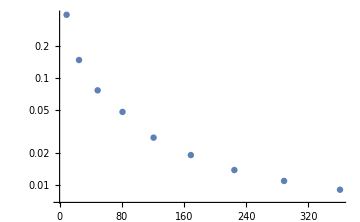

```mathematica
(* Test poly decay, using a LogLog plot: *)
Show[{
ListLogLogPlot[ { squareScalingRnd}, Joined -> False ] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

(* Test Exp decay *)
Show[{
ListLogPlot[{ squareScalingRnd}, Joined->False]
}]
```

#### Random BIP graphs

```mathematica
(* NOTE: This construction causes multiple random bip graphs to be constructed, per value of v1  *) 
vs = Round[ Range[2,100, .02] ]; 
brange = {1};
p = .81;
nsamps = 20;

bipnqfun[v1_,b_ ]:= 2 v1 - 1;
bipgraphfun[v1_, b_ ] := RandBipGraph[ v1, p ][[1]];

bipScalingRnd  = graphGapScaling[ bipgraphfun, bipnqfun, vs,brange, nsamps ];
bipScaling =  graphGapScaling[ bipgraphfun, bipnqfun, vs, brange, 1 ];
```

```mathematica
(* Average over the various generated edge configurations *)
allNs = DeleteDuplicates[ bipScalingRnd[[All,1]] ];
bipRndAvgs = {};
bipRndStdevs ={};
Do[ 
fixedN = Select[bipScalingRnd, #[[1]] == allNs[[j]] & ] ;
AppendTo[ bipRndAvgs, {allNs[[j]], Mean[ fixedN[[All,2]] ]} ] ;
AppendTo[ bipRndStdevs, {allNs[[j]], StandardDeviation[ fixedN[[All,2]] ]} ];
, {j, 1, Length[allNs]}];
upbnd = Table[ { bipRndAvgs[[j,1]], bipRndAvgs[[j,2]] + bipRndStdevs[[j,2]] }, {j,1,Length[bipRndAvgs]}];
lowbnd = Table[ { bipRndAvgs[[j,1]], bipRndAvgs[[j,2]] - bipRndStdevs[[j,2]] }, {j,1,Length[bipRndAvgs]}];
```

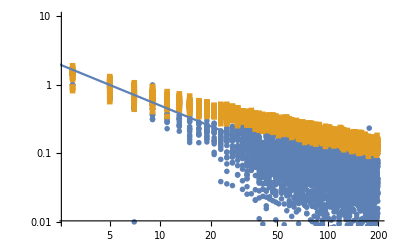

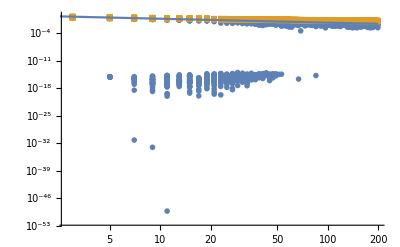

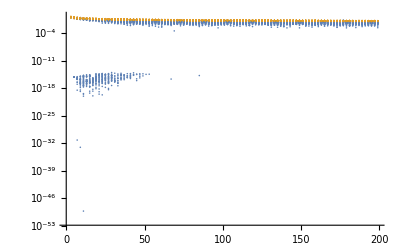

```mathematica
(* Test poly decay, using a LogLog plot: *)
Show[{
ListLogLogPlot[ { bipScaling,bipScalingRnd}, Joined -> False , PlotRange->{10^-2,10}] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

Show[{
ListLogLogPlot[ { bipScaling,bipScalingRnd}, Joined -> False, PlotRange->All] 
,LogLogPlot[ 5 * 1/x , {x,1,200 } ]
}]

(* Test Exp decay *)
Show[{
ListLogPlot[{ bipScaling, bipScalingRnd}, Joined->False]
}]
```

#### Tree graphs, using an efficient method

```mathematica
depthToNQ[ depth_ ]:= 1 + Sum[ 2 * 2^k , {k,1,depth}];
diameterToDepth[ diam_ ] := diam/2 - 1;

binTreeGap[ diam_ ]:= Module[{g0, g1, ev0, ev1},
g0 =  DiagonalMatrix[ Join @@ ConstantArray[ { 1, 2 }, Floor[diam/2] ] , +1 ] + DiagonalMatrix[ ConstantArray[ 1, diam-1 ] , -1];
g1 = g0[[;;-2, ;;-2]];

ev0 = Sort[ Eigenvalues[ N@g0 ]   ][[  Ceiling[ diam/ 2 ]  + 1 ]];
ev1 = Sort[ Eigenvalues[ N@g1 ]   ][[  Floor[ diam/ 2 ]  + 1 ]];
Return[{depthToNQ@diameterToDepth[ diam ], Min[ ev0, ev1 ]  }]
];
```

```mathematica
diameters = Range[ 5, 40, 4  ];
treegapscaling = Table[ binTreeGap[ diam ], {diam, diameters} ]
```

{{5,0.517638},{29,0.200777},{125,0.0922773},{509,0.0448218},{2045,0.0221953},{8189,0.0110634},{32765,0.00552647},{131069,0.00276245},{524285,0.00138111}}

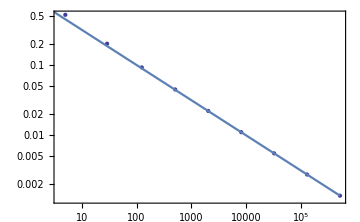

```mathematica
Show[{
ListLogLogPlot[treegapscaling, Joined->False ]
, LogLogPlot[ x^-(1/2), {x,1,Max[treegapscaling[[All,1]] ]} ]
}]
```

### Plotting all gaps together

#### Silly save of data

```mathematica
{ upbnd, lowbnd, squareScalingRnd, hexScaling, starScaling, treegapscaling} = {{{3,1.7049929494697063},{5,1.2196373817851203},{7,0.9091828931280553},{9,0.7915463587811749},{11,0.6833598447423821},{13,0.6383331133375945},{15,0.5646706344050899},{17,0.5380334235698022},{19,0.514271953262201},{21,0.46470758743375223},{23,0.4529891673293586},{25,0.438253650425297},{27,0.4128652624823938},{29,0.39718873180429143},{31,0.3845043512652266},{33,0.3744158184828581},{35,0.36863777327941244},{37,0.33879171516234396},{39,0.3396393942817279},{41,0.32353401881237703},{43,0.32130935910041464},{45,0.3151615019738382},{47,0.30490116635513664},{49,0.2989570658437755},{51,0.293178819404517},{53,0.28530039769397836},{55,0.2831144005513525},{57,0.2845239747439231},{59,0.2802877804806779},{61,0.26827118552132534},{63,0.2673886719050014},{65,0.2677728426348367},{67,0.25742466955192805},{69,0.25250588212589586},{71,0.2512566763825095},{73,0.2436127418341092},{75,0.23876894956660744},{77,0.24045162017150246},{79,0.2328297405024029},{81,0.2332107324795738},{83,0.229930447757747},{85,0.23100735107873396},{87,0.21982040993748905},{89,0.2200009979264286},{91,0.21579618650554055},{93,0.21224177550216236},{95,0.2036614582433225},{97,0.2103295753682793},{99,0.2115183981001768},{101,0.20982948980487762},{103,0.2053480742590189},{105,0.1997990557894211},{107,0.20071262223671044},{109,0.1993208906786429},{111,0.1977393673074183},{113,0.19670622737559468},{115,0.19062771796439076},{117,0.19637601850022957},{119,0.19424844020475557},{121,0.1860912660957801},{123,0.18689662989324965},{125,0.18258095132267096},{127,0.18566014455645885},{129,0.18400834817052286},{131,0.18280575116963463},{133,0.17506251451806537},{135,0.18267968632070905},{137,0.1762416968308503},{139,0.1725417413853},{141,0.16976747831288244},{143,0.17853537104299455},{145,0.177272262891031},{147,0.17708185000613888},{149,0.17260847298114865},{151,0.16504145968559905},{153,0.1689321403206334},{155,0.16527228261344454},{157,0.16711485608915164},{159,0.17347749643789845},{161,0.16047694070842441},{163,0.1632286958963677},{165,0.1617864137546765},{167,0.1571699885880115},{169,0.15652378352805713},{171,0.1543927498911126},{173,0.15614675988285648},{175,0.1594554228810724},{177,0.1533240588098494},{179,0.15196857699952807},{181,0.15599244228079692},{183,0.15334590272603926},{185,0.15006879819152513},{187,0.15331262761109565},{189,0.14801948864179001},{191,0.15201402112061196},{193,0.1482766504218581},{195,0.14519714302740244},{197,0.15256108600234297},{199,0.14948482919760323}},{{3,1.1529294818180418},{5,0.6963962778621078},{7,0.6243286323705456},{9,0.5790351057112435},{11,0.4992630869062123},{13,0.49593844661615294},{15,0.45120163934252094},{17,0.4282641924806998},{19,0.40035688901534583},{21,0.37364557459408726},{23,0.3549460253821231},{25,0.33065505704483794},{27,0.31857149827496395},{29,0.30073362507646645},{31,0.3084382531581665},{33,0.2897631439668408},{35,0.2892167814696545},{37,0.27143089578368695},{39,0.27351324362506496},{41,0.258411402667528},{43,0.25472316860467376},{45,0.24650709588393094},{47,0.23991037975390805},{49,0.23587726663308534},{51,0.22602652394064077},{53,0.2305185515022778},{55,0.22121448261131138},{57,0.22156648479095656},{59,0.22866994502215973},{61,0.21323192211249947},{63,0.21075713040250663},{65,0.22191352859528019},{67,0.20358129326292115},{69,0.1951812277318882},{71,0.20113038016359722},{73,0.19146322026953633},{75,0.19106374156520456},{77,0.18492432815115972},{79,0.1790337713177066},{81,0.17357461084213643},{83,0.1779566308435563},{85,0.16805599602463797},{87,0.17731166693138958},{89,0.1747851799682876},{91,0.17205758773646657},{93,0.1709233376604711},{95,0.16906153706012106},{97,0.16352822732374184},{99,0.16717186952290486},{101,0.16191887206076735},{103,0.1615029615040442},{105,0.16153783584680176},{107,0.1623741916676435},{109,0.1572540945643775},{111,0.156635635349268},{113,0.15732597715491453},{115,0.15263303109010118},{117,0.15202199899263263},{119,0.15492551089387085},{121,0.1450136140463826},{123,0.14627299432706317},{125,0.1430292451317147},{127,0.14851897075564674},{129,0.14715424989776354},{131,0.1443253667498652},{133,0.14270460813490066},{135,0.1413830463923564},{137,0.14291563884589356},{139,0.13407659973482064},{141,0.13795142280244224},{143,0.13434277224554686},{145,0.1340329032516183},{147,0.1349947411195818},{149,0.13368035614814702},{151,0.1327715734003008},{153,0.13277192255299333},{155,0.13224063190542282},{157,0.1288139091401124},{159,0.1341212568970485},{161,0.1275865737076937},{163,0.13004071178817864},{165,0.12629171916243115},{167,0.12196181132010053},{169,0.12342107814445702},{171,0.1262813894200319},{173,0.12459444302613837},{175,0.12255278763687416},{177,0.12253961879683446},{179,0.11950995411423296},{181,0.12673835107768364},{183,0.12175241096634944},{185,0.12533891322372925},{187,0.1229051789845933},{189,0.11773930789252443},{191,0.11968953753407069},{193,0.11535664795031769},{195,0.11893810307722358},{197,0.11996392645731178},{199,0.12072454264969308}},{{9,0.3889000840928729},{25,0.1468677462347301},{49,0.07646032828822992},{81,0.048045459930150136},{121,0.027612168006420672},{169,0.018972550997819818},{225,0.01374452348846281},{289,0.010867299462799174},{361,0.008999419237687803}},{{7,1.},{17,0.445041867912629},{31,0.18588534642645946},{49,0.07110959738148799},{71,0.024996352060692412},{97,0.008241295463844162},{127,0.0025977928648598216},{161,0.0007929660636490172},{199,0.00023629433062235408},{241,0.00006910488084127437},{287,0.000019907806932574255},{337,5.6644877887678336*^-6},{391,1.5951234186572084*^-6},{449,4.4524482722513757*^-7},{511,1.2334076011238012*^-7},{577,3.394260260276917*^-8},{647,9.286742525128253*^-9},{721,2.527841779299416*^-9},{799,6.849298572459706*^-10}},{{7,1.},{13,0.6180339887498945},{19,0.44504186791262784},{25,0.3472963553338603},{31,0.2846296765465697},{37,0.2410733605106461},{43,0.20905692653530647},{49,0.18453671892660395},{55,0.16515869094466398},{61,0.14946018717284848},{91,0.10129833767742519},{121,0.07660546738006857},{151,0.06159011711234056},{181,0.05149582730997699}},{{5,0.5176380902050416},{29,0.20077714309435013},{125,0.0922773014904335},{509,0.04482179317941678},{2045,0.022195343690829906},{8189,0.011063431745619145},{32765,0.005526465636128116},{131069,0.0027624520593047827},{524285,0.0013811127167856698}}};
```

```mathematica
upbnd
```

{{3,1.70499},{5,1.21964},{7,0.909183},{9,0.791546},{11,0.68336},{13,0.638333},{15,0.564671},{17,0.538033},{19,0.514272},{21,0.464708},{23,0.452989},{25,0.438254},{27,0.412865},{29,0.397189},{31,0.384504},{33,0.374416},{35,0.368638},{37,0.338792},{39,0.339639},{41,0.323534},{43,0.321309},{45,0.315162},{47,0.304901},{49,0.298957},{51,0.293179},{53,0.2853},{55,0.283114},{57,0.284524},{59,0.280288},{61,0.268271},{63,0.267389},{65,0.267773},{67,0.257425},{69,0.252506},{71,0.251257},{73,0.243613},{75,0.238769},{77,0.240452},{79,0.23283},{81,0.233211},{83,0.22993},{85,0.231007},{87,0.21982},{89,0.220001},{91,0.215796},{93,0.212242},{95,0.203661},{97,0.21033},{99,0.211518},{101,0.209829},{103,0.205348},{105,0.199799},{107,0.200713},{109,0.199321},{111,0.197739},{113,0.196706},{115,0.190628},{117,0.196376},{119,0.194248},{121,0.186091},{123,0.186897},{125,0.182581},{127,0.18566},{129,0.184008},{131,0.182806},{133,0.175063},{135,0.18268},{137,0.176242},{139,0.172542},{141,0.169767},{143,0.178535},{145,0.177272},{147,0.177082},{149,0.172608},{151,0.165041},{153,0.168932},{155,0.165272},{157,0.167115},{159,0.173477},{161,0.160477},{163,0.163229},{165,0.161786},{167,0.15717},{169,0.156524},{171,0.154393},{173,0.156147},{175,0.159455},{177,0.153324},{179,0.151969},{181,0.155992},{183,0.153346},{185,0.150069},{187,0.153313},{189,0.148019},{191,0.152014},{193,0.148277},{195,0.145197},{197,0.152561},{199,0.149485}}

```mathematica
lowbnd
```

{{3,1.15293},{5,0.696396},{7,0.624329},{9,0.579035},{11,0.499263},{13,0.495938},{15,0.451202},{17,0.428264},{19,0.400357},{21,0.373646},{23,0.354946},{25,0.330655},{27,0.318571},{29,0.300734},{31,0.308438},{33,0.289763},{35,0.289217},{37,0.271431},{39,0.273513},{41,0.258411},{43,0.254723},{45,0.246507},{47,0.23991},{49,0.235877},{51,0.226027},{53,0.230519},{55,0.221214},{57,0.221566},{59,0.22867},{61,0.213232},{63,0.210757},{65,0.221914},{67,0.203581},{69,0.195181},{71,0.20113},{73,0.191463},{75,0.191064},{77,0.184924},{79,0.179034},{81,0.173575},{83,0.177957},{85,0.168056},{87,0.177312},{89,0.174785},{91,0.172058},{93,0.170923},{95,0.169062},{97,0.163528},{99,0.167172},{101,0.161919},{103,0.161503},{105,0.161538},{107,0.162374},{109,0.157254},{111,0.156636},{113,0.157326},{115,0.152633},{117,0.152022},{119,0.154926},{121,0.145014},{123,0.146273},{125,0.143029},{127,0.148519},{129,0.147154},{131,0.144325},{133,0.142705},{135,0.141383},{137,0.142916},{139,0.134077},{141,0.137951},{143,0.134343},{145,0.134033},{147,0.134995},{149,0.13368},{151,0.132772},{153,0.132772},{155,0.132241},{157,0.128814},{159,0.134121},{161,0.127587},{163,0.130041},{165,0.126292},{167,0.121962},{169,0.123421},{171,0.126281},{173,0.124594},{175,0.122553},{177,0.12254},{179,0.11951},{181,0.126738},{183,0.121752},{185,0.125339},{187,0.122905},{189,0.117739},{191,0.11969},{193,0.115357},{195,0.118938},{197,0.119964},{199,0.120725}}

```mathematica
squareScalingRnd
```

{{9,0.3889},{25,0.146868},{49,0.0764603},{81,0.0480455},{121,0.0276122},{169,0.0189726},{225,0.0137445},{289,0.0108673},{361,0.00899942}}

```mathematica
hexScaling
```

{{7,1.},{17,0.445042},{31,0.185885},{49,0.0711096},{71,0.0249964},{97,0.0082413},{127,0.00259779},{161,0.000792966},{199,0.000236294},{241,0.0000691049},{287,0.0000199078},{337,5.66449×10^-6},{391,1.59512×10^-6},{449,4.45245×10^-7},{511,1.23341×10^-7},{577,3.39426×10^-8},{647,9.28674×10^-9},{721,2.52784×10^-9},{799,6.8493×10^-10}}

```mathematica
starScaling
```

{{7,1.},{13,0.618034},{19,0.445042},{25,0.347296},{31,0.28463},{37,0.241073},{43,0.209057},{49,0.184537},{55,0.165159},{61,0.14946},{91,0.101298},{121,0.0766055},{151,0.0615901},{181,0.0514958}}

```mathematica
treegapscaling
```

{{5,0.517638},{29,0.200777},{125,0.0922773},{509,0.0448218},{2045,0.0221953},{8189,0.0110634},{32765,0.00552647},{131069,0.00276245},{524285,0.00138111}}

#### All together

```mathematica
blend = .5;
elementarycols = {Darker@Red, Darker@Darker@Green,  Blend[  {Darker@Red, Yellow},blend ], Blend[ {Darker@Darker@Green, Blue}, blend ], Purple };

markers = Graphics`PlotMarkers[];
markers[[All,2]] = markers[[All,2]]*1.8;

SetOptions[ ListLogLogPlot
, BaseStyle -> {FontFamily-> Times, FontSize-> 12}
,Axes -> {False, False} 
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.004 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 11, Black ]
, FrameTicks-> Automatic
, ImageSize-> Medium
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.005] ]
, PlotMarkers -> None
, Joined -> True
];
```

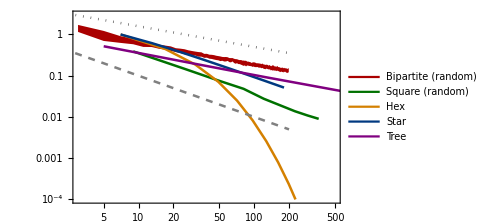

```mathematica
pltstyle = Join[
Table[ Directive[ Opacity[0], Thickness[0] ], 2 ] (* First entry is doubled *)
 , Table[  Directive[ elementarycols[[j]], Thickness[0.005] ], {j,2,Length[elementarycols]}]
];
filstyle = elementarycols[[1]];

(* Legend: TODO: arrows, for black/white printing? *)
legdescr = {"Bipartite (random)", "Square (random)",  "Hex", "Star", "Tree"};
leg = LineLegend[ elementarycols, legdescr ];

evalgapsplt = Show[{
ListLogLogPlot[ { upbnd, lowbnd, squareScalingRnd, hexScaling, starScaling, treegapscaling}
 ,PlotRange->{ {3,500}, {10^-4, 3}}
, PlotStyle->pltstyle 
, FrameLabel-> {MaTeX["|V|", Magnification->1.5], MaTeX["\\Delta E", Magnification->1.5]}
, Filling -> {1 -> {2} }
, FillingStyle-> filstyle
, PlotLegends->leg
]
,LogLogPlot[ {1 * x^{-1}, 5 x^(-1/2) } , {x,1,200 } , PlotStyle->{ Directive[Gray, Dashed, Thickness[0.005] ], Directive[ Darker@Gray, Dotted, Thickness[0.005] ] }]
}]
```

```mathematica
Export[ "evalgaps.pdf", evalgapsplt ]
```

evalgaps.pdf

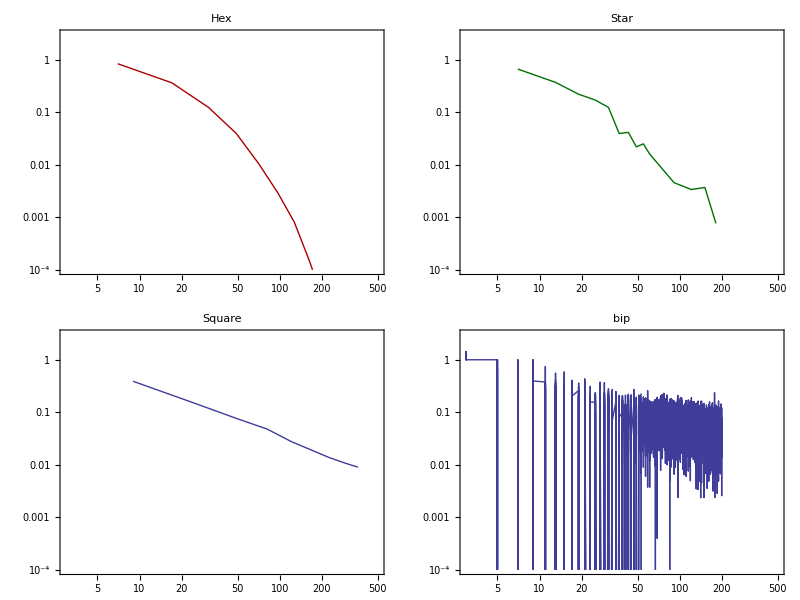

```mathematica
plts =  {hexScalingRnd, starScalingRnd, squareScalingRnd, bipScaling};
descr = {"Hex", "Star", "Square", "bip"};
pltstyle = Table[  Directive[ elementarycols[[j]] ], {j,1,Length[elementarycols]}];

plttab = Grid@ArrayReshape[#, {2,2}]& @ Table[
ListLogLogPlot[ plts[[j]], PlotRange->{ {3,500}, {10^-4, 3}} , PlotStyle ->  pltstyle[[j]], PlotLabel->descr[[j]]  ]

,{ j, 1,Length@ plts}]
```

### Statistics on the gap.... Seems that small gaps are more common :(.

```mathematica
makegraph[w_,h_]:= perturbHermitean[ AdjacencyMatrix@GridGraph[ {w,h} ], {0,2} ];
p1s = {3};
p2s = {3};
giveaidx[p1_,p2_]:= 1;
givebidx[p1_,p2_]:= p1*p2;
Ts = {50,100};

sqgriderr = CTAPerrorMulti[ makegraph, p1s, p2s, giveaidx, givebidx, Ts ];
```

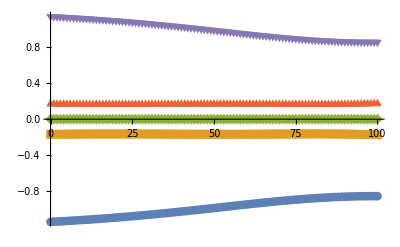

```mathematica
gapstatistic = Table[

g = makegraph[3,3];
T=100;
afun = t/T; bfun = 1-t/T;
g[[1,All]] *= afun;
g[[All,1]] *= afun;
g[[-1,All]] *= bfun;
g[[All,-1]] *= bfun;
evalvsT = evalTimePlot[ Normal@g, {t,0,T} ];
evalvsT[[6,-1,2]] 
,{1000}];

ListPlot[evalvsT[[ 3;;7]] ]
```

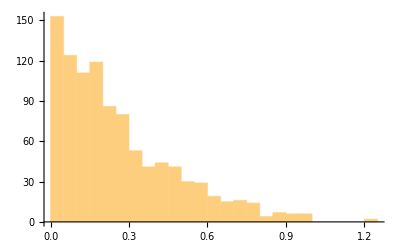

```mathematica
Histogram[gapstatistic, 20]
```

# Transfer error vs graph size

```mathematica
CTAPerrorSingle[ ham_, aidx_, bidx_,{t_,Ti_, Tf_} ] := Module[{nq, state, err},

	nq = Length[ham];
	state = Normalize@evolveState[ ham, Vec[aidx-1, nq] ,{t,Ti, Tf}][Tf];
	err = 1-Abs[state.Vec[bidx-1, nq]];
	Return[err];
];

CTAPerrorMulti[ makeGraph_, p1s_, p2s_, giveaidx_, givebidx_, Ts_, nsamps_:1 ]:= Module[{afun, bfun, aidx, bidx, ham, t, fixparres},

	afun[t_, T_] := t/T;
	bfun[t_, T_] := 1-t/T;

	res = Table[  (* Loop over p1/p2 *)
		aidx = giveaidx[ p1, p2];
		bidx = givebidx[ p1, p2];
		
		Table[ (* Loop over Ts *)
		
			fixparres = Table[ (* results over many loops (samples), for fixed parameters *)
				ham = makeGraph[p1, p2];
				ham[[aidx,All]] *= afun[t,T];
				ham[[All,aidx]] *= afun[t,T];
				ham[[bidx,All]] *= bfun[t,T];
				ham[[All,bidx]] *= bfun[t,T];
				CTAPerrorSingle[ ham, aidx, bidx, {t,0,T} ]
			,{nsamps}];
			
			{p1, p2, T, Mean@fixparres, StandardDeviation[fixparres] }
			
		,{T,Ts}]
	,{p1,p1s}, {p2,p2s}];

	Return[res];

];

(* Assume the data has the shape (p1, T, error), and also each entry has structute (p1, T, error)
	TODO adjust for (p1, p2, T, error) *)
findTargetTimes[ dataArray_, targetEr_ ]:=Table[
	filtered = Select[dataArray[[j]], #[[3]] ≤ targetEr & ] ;
	bestT = Min[ filtered[[All,2]] ];
	{dataArray[[j,1,1]], bestT}
,{j, 1, Length@dataArray}];

(* Assuming a flattened array with entries (p1, T, error), find for each p1 the optimal T *)
findTargetTimesFlat[ dataList_, targetEr_ ]:= Module[{allparams, filtered, bestT},
	
	allparams = DeleteDuplicates[ dataList[[All,1]] ];
	Return[ Table[
		filtered = Select[ dataList, #[[1]] == allparams[[j]] && #[[3]] ≤ targetEr & ];
		bestT = Min[ filtered[[All,2]] ];
		{allparams[[j]], bestT}
	,{j,1,Length[allparams]}] ];
];
```

#### Star graph: How much time needed to reach 5% accuracy?

Still uses old functions... would rather generalize to the new types of function that take as input “makegraph”.

```mathematica
simulationErrorStar[ narms_, larms_, T_, wafun_, wbfun_ ] := Module[ {g,l,w,nq,uniformParams,wa,wb,setwa,setwb,hamt,state,err},
	{g,l} = starGraph[narms, larms, w  ];
	nq = narms*larms + 1;

	uniformParams = Table[ p -> 1, {p,l} ];
	wa = {w[1,2]};
	wb = Table[ i = larms+ m * larms ; w[i, nq] , {m,0, narms-1} ];
	
	(* Use this for transporting to arm number 2: *)
	(* wb = Table[  w[ larms+1, larms+2 ] , {m,0, narms-1} ]; (* CHANGE HERE *) *)

	setwa = Table[ p -> wafun , {p,wa}];
	setwb = Table[ p -> wbfun , {p, wb} ];

	hamt = g /. setwa /. setwb /. uniformParams;
	state = evolveState[ hamt, Vec[0,nq], {t,0,T} ][T];
	err = 1- Abs[state.Vec[nq-1,nq]]; (* No conjugation needed for basis state |nq> *)

	(* Use this for transporting to arm number 2: *)
	(* err = 1- Abs[state.Vec[larms,nq]]; (* CHANGE HERE! *) *)

	Return[err];
];
```

Loop over various narms and larms

```mathematica
narmss = Range[2,10];
larmss = Range[2,8,2];
Ts = Table[ 2^x, {x,2,8,.2} ];
targetEr = 0.01;  (* WATCH THIS PARAMETER! It's still open -- as of 29/01, the paper says 0.05 *)



(* res had dimensions (narms, Ts, 3 ) *)
Table[
ErvsNarms[larms] = Table[
wafun = t/T;
wbfun = 1-t/T;
{narms, T, simulationErrorStar[ narms, larms, T, wafun, wbfun ]}
,{narms, narmss}, {T, Ts}];
,{larms, larmss}];
```

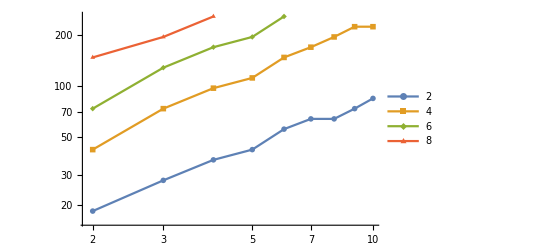

```mathematica
targetTimes = Table[ findTargetTimes[ ErvsNarms[larms], targetEr ], {larms, larmss} ];
pltStarTvsArms = ListLogLogPlot[targetTimes, PlotLegends->larmss, FrameLabel->{"# arms", "T"}]
```

```mathematica
Export[ "pltStarvsArms.pdf", pltStarTvsArms ]
```

pltStarvsArms.pdf

A better representation: FID vs NQ, where we still keep information about larms (the different numbers in the legend).

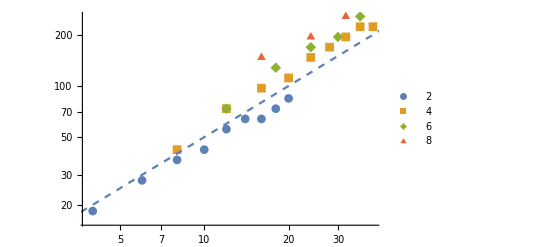

```mathematica
targetTimesvsNQ = Table[
tmp = targetTimes[[j]];
tmp[[All,1]] = larmss[[j]] * tmp[[All,1]];
tmp
,{j,1,Length@larmss}];

pltStarTvsNQ = Show[{
 ListLogLogPlot[targetTimesvsNQ, PlotLegends->larmss, FrameLabel->{MaTeX["|V|"], MaTeX["T^*"]}, Joined-> False, PlotMarkers -> Automatic]
, LogLogPlot[ 5 n, {n,0,50} , PlotStyle->Dashed]
}]
```

```mathematica
Export[ "pltStarvsNQ.pdf", pltStarTvsNQ ]
```

pltStarvsNQ.pdf

#### Square Graphs: How much time needed to reach 5% accuracy?

IMPORTANT: The square grid has multiple 0 eigenvalues.... luckily our choice of time-dependent weights happens to be “just right”.

```mathematica
makegraph[w_,h_]:= perturbHermitean[ AdjacencyMatrix@GridGraph[ {w,h} ], {0,2} ];
p1s = {3,5,7,9};
p2s = {3};
giveaidx[p1_,p2_]:= 1;
givebidx[p1_,p2_]:= 3;
Ts = 2^Range[2,9,.2];
nsamps = 100;

sqgriderr = CTAPerrorMulti[ makegraph, p1s, p2s, giveaidx, givebidx, Ts,  10];
```

```mathematica
sqerrflat = ArrayReshape[ sqgriderr, { Length[p1s] * Length[p2s] * Length[Ts], Length[sqgriderr[[1,1,1]] ]} ];
(* The following list contains: (nq, T, mean_error) *)
sqErrvsNq = Table[ {e[[1]] * e[[2]], e[[3]], e[[4]]}, {e,sqerrflat} ];
```

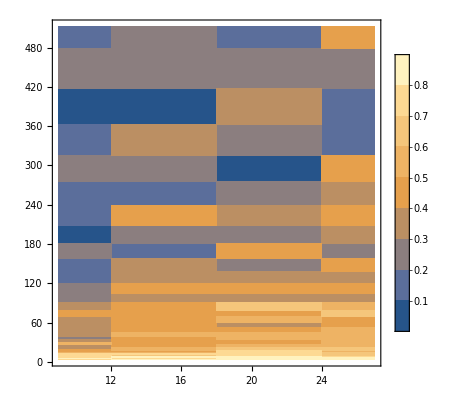

```mathematica
ListContourPlot[ sqErrvsNq, InterpolationOrder->0, PlotLegends->Automatic ]
```

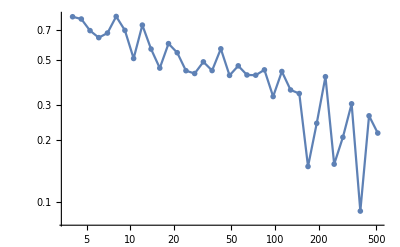

```mathematica
ListLogLogPlot[ Select[ sqerrflat, #[[1]] == 5 & ][[All,{3,4} ]] ]
```

```mathematica
temp = sqgriderr[[All,2,All,{1,3,4}]];
```

```mathematica
findTargetTimes[ temp, 0.5 ]
```

{{3,16.},{5,64.},{7,32.},{9,64.}}